```mathematica
Subscript[A, m][V_]:=(0.1*(25-V))/(E^((25-V)/10)-1)

Subscript[B, m][V_]:=4*E^(-V/18)
Subscript[A, h][V_]:=0.07*E^(-V/20)
Subscript[B, h][V_]:= 1/(E^((30-V)/10)+1)
Subscript[A, n][V_]:= (0.01*(10-V))/(E^((10-V)/10)-1)
Subscript[B, n][V_]:= 0.125*E^(-V/80)
```

```mathematica
Subscript[m, 0][V_]:=(Subscript[A, m][V])/(Subscript[A, m][V]+Subscript[B, m][V])
```

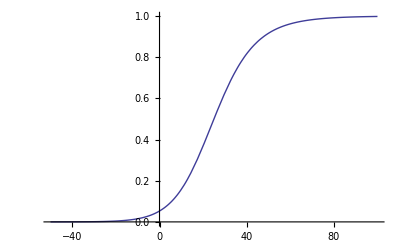

```mathematica
Plot[Subscript[m, 0][V],{V,-50,100}]
```

```mathematica
Subscript[h, 0][V_]:=(Subscript[A, h][V])/(Subscript[A, h][V]+Subscript[B, h][V])
```

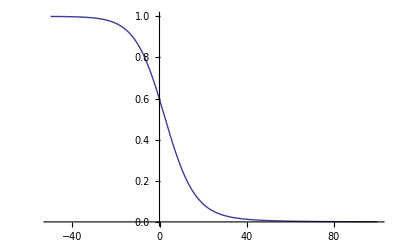

```mathematica
Plot[Subscript[h, 0][V],{V,-50,100}]
```

```mathematica
Subscript[n, 0][V_]:=Subscript[A, n][V]/(Subscript[A, n][V]+Subscript[B, n][V])
```

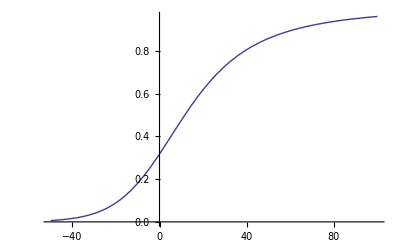

```mathematica
Plot[Subscript[n, 0][V],{V,-50,100}]
```

```mathematica
Subscript[G, Na]=120
Subscript[G, K]=34
Subscript[G, L]=0.26
Subscript[V, Na]=109
Subscript[V, K]=-11
Subscript[V, L]=11
```

120

34

0.26

109

-11

11

```mathematica
Subscript[T, m][V_]:=1/(Subscript[A, m][V]+Subscript[B, m][V])
```

```mathematica
Subscript[T, h][V_]:=1/(Subscript[A, h][V]+Subscript[B, h][V])
```

```mathematica
Subscript[T, n][V_]:=1/(Subscript[A, n][V]+Subscript[B, n][V])
```

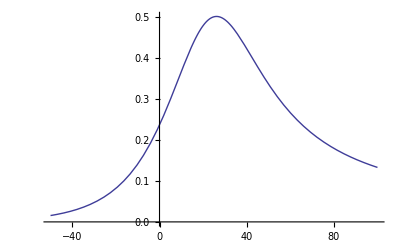

```mathematica
Plot[Subscript[T, m][V],{V,-50,100}]
```

```mathematica
Plot[Subscript[T, h][V],{V,-50,100}]
```

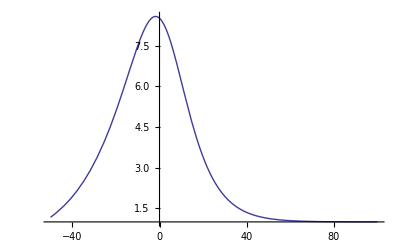

```mathematica
Plot[Subscript[T, n][V],{V,-120,100}]
```

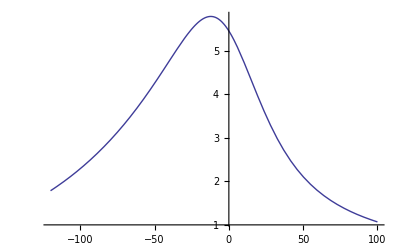

```mathematica
M=DSolve[{m'[t]==-(m[t]-Subscript[m, 0][15])/(Subscript[T, m][15]),m[0]==0},m,t]
```

{{m→Function[{t},0.250812 ⅇ^(-2.32037 t) (-1.+1. ⅇ^(2.32037 t))]}}

```mathematica
V=25;
```

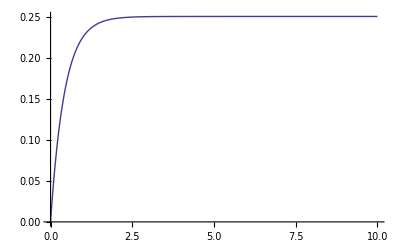

```mathematica
Plot[m[t]/.M[[1]],{t,0,10},PlotRange->All]
```

```mathematica
P=DSolve[{m'[t]==-(m[t]-Subscript[m, 0][60])/(Subscript[T, m][60]),m[0]==0},m,t]
```

{{m→Function[{t},0.961965 ⅇ^(-3.75168 t) (-1.+1. ⅇ^(3.75168 t))]}}

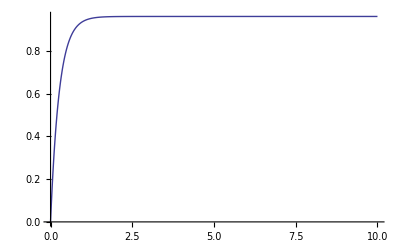

```mathematica
Plot[m[t]/.P[[1]],{t,0,10},PlotRange->All]
```

```mathematica
HD=DSolve[{h'[t]==-(h[t]-Subscript[h, 0][60])/(Subscript[T, h][60]),h[0]==1},h,t]
```

{{h→Function[{t},0.00364527 ⅇ^(-0.956059 t) (273.328+1. ⅇ^(0.956059 t))]}}

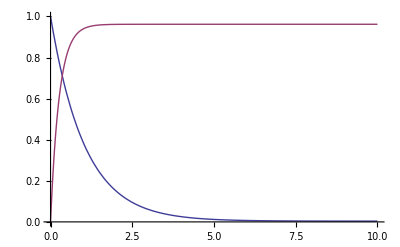

```mathematica
Plot[{h[t]/.HD[[1]],m[t]/.P[[1]]},{t,0,10},PlotRange->All]
```

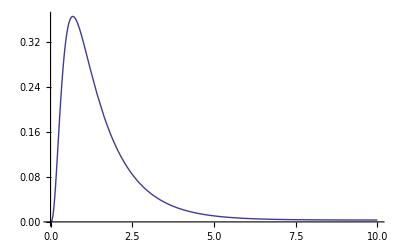

```mathematica
Plot[(h[t]/.HD[[1]])*(m[t]/.P[[1]])^3,{t,0,10},PlotRange->All]
```

```mathematica
HD15=DSolve[{h'[t]==-(h[t]-Subscript[h, 0][15])/(Subscript[T, h][15]),h[0]==1},h,t]
```

{{h→Function[{t},0.153443 ⅇ^(-0.215491 t) (5.51707+1. ⅇ^(0.215491 t))]}}

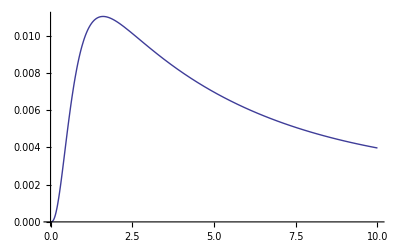

```mathematica
Plot[(h[t]/.HD15[[1]])*(m[t]/.M[[1]])^3,{t,0,10},PlotRange->All]
```

```mathematica
ND15=DSolve[{n'[t]==-(n[t]-Subscript[n, 0][15])/(Subscript[T, n][15]),n[0]==0},n,t]
```

{{n→Function[{t},0.550814 ⅇ^(-0.230703 t) (-1.+1. ⅇ^(0.230703 t))]}}

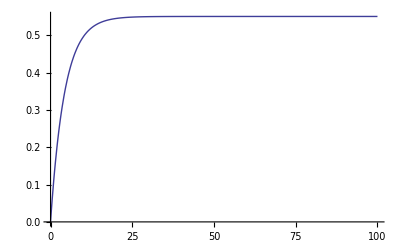

```mathematica
Plot[n[t]/.ND15[[1]],{t,0,100},PlotRange->All]
```

```mathematica
NDn20=DSolve[{n'[t]==-(n[t]-Subscript[n, 0][-20])/(Subscript[T, n][-20]),n[0]==0},n,t]
```

{{n→Function[{t},0.0891984 ⅇ^(-0.176222 t) (-1.+1. ⅇ^(0.176222 t))]}}

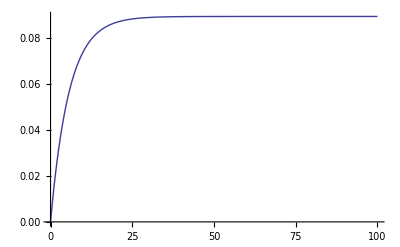

```mathematica
Plot[n[t]/.NDn20[[1]],{t,0,100},PlotRange->All]
```

```mathematica
ND60=DSolve[{n'[t]==-(n[t]-Subscript[n, 0][60])/(Subscript[T, n][60]),n[0]==0},n,t]
```

{{n→Function[{t},0.895018 ⅇ^(-0.562438 t) (-1.+1. ⅇ^(0.562438 t))]}}

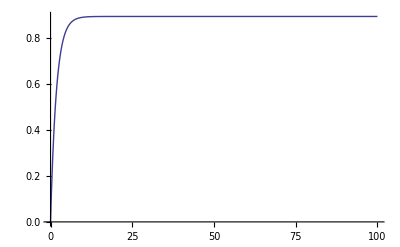

```mathematica
Plot[n[t]/.ND60[[1]],{t,0,100},PlotRange->All]
```

```mathematica
Subscript[J, ion][t_]:=Subscript[G, Na]*(m[t]/.P[[1]])^3*(h[t]/.HD[[1]])*(60-Subscript[V, Na])+Subscript[G, K]*(n[t]/.ND60[[1]])^4*(60-Subscript[V, K])+Subscript[G, L]*(60-Subscript[V, L]);

Subscript[J, ion15][t_]:=Subscript[G, Na]*(m[t]/.M[[1]])^3*(h[t]/.HD15[[1]])*(15-Subscript[V, Na])+Subscript[G, K]*(n[t]/.ND15[[1]])^4*(15-Subscript[V, K])+Subscript[G, L]*(15-Subscript[V, L]);
```

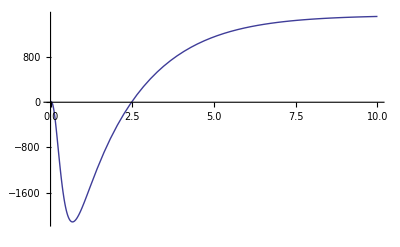

```mathematica
Plot[Subscript[J, ion][t],{t,0,10},PlotRange->All]
```

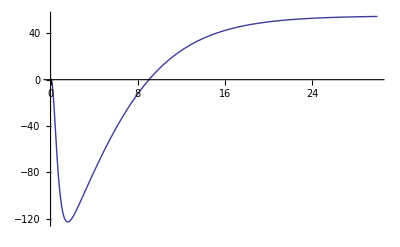

```mathematica
Plot[Subscript[J, ion15][t],{t,0,30},PlotRange->All]
```